# title

## 1

```mathematica
ClearAll["`*"]
```

```mathematica
πspt=p∫_0^(((1-τpt)w qpt)/p) (1-F[D])ⅆD+τpt w qpt-c qpt;
πsis=p∫_0^((w qi-yi)/p) (1-F[D])ⅆD-c qi+(1-h)yi;
F[x_]:=x
Fm1[x_]:=x
```

```mathematica
πspt1=πspt/.qpt->(p (p-w))/(p^2-w^2 (-1+τpt)^2)//FullSimplify;
```

for region c>c_2=1/2(3w-1) , the supplier’s profit function is

```mathematica
πspt11=πspt1/.τpt->1//FullSimplify
```

((p-w) (-c+w))/p

for region c_1≤c≤c_2 , c_1=1/2(1+w-2/(1+w))  the supplier’s profit function is

```mathematica
πspt12=πspt1/.τpt->1-p/w √((3w-p-2c)/(-2c+p+w))//FullSimplify
```

(-2 c+p+w)^2/(8 p)

Under IS strategy , the supplier’s profit function

```mathematica
πsis1=πsis/.{qi->(p (p-w))/(p^2-w^2),yi->w (p (p-w))/(p^2-w^2)-p Fm1[h]}//FullSimplify
```

(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))

#### in the region that τpt^*=1

if PT strategy better than IS strategy, then

```mathematica
aa1=πspt11-πsis1//FullSimplify
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))

```mathematica
-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))

```mathematica
Solve[aa1==0,c]//FullSimplify
```

{{c→-(h p^2)/w+w+(h^2 p^2 (p+w))/(2 w^2)}}

if PT>IS,  c> c_a(h,p,w)=-(h p^2)/w+w+(h^2 p^2 (p+w))/(2 w^2)

```mathematica
Solve[aa1==0,h]//FullSimplify
```

{{h→(w (p-√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))},{h→(w (p+√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))}}

```mathematica
Manipulate[{(w (p-√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w)),(w (p+√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))},{p,1,1},{c,0,1},{w,0,1}];
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))>0,   (h p w)/(p+w)>(h^2 p)/2+((w-c) w^2)/(p (p+w)),  h> (h^2 p)/2*(p+w)/(p w)+((w-c) w^2)/(p (p+w))(p+w)/(p w)=h^2/2*(p+w)/w+((w-c) w)/p^2=h_a(h,w,c)

c>c_2(w)   h>h_a(h,w,c)

```mathematica
c1=1/2(1+w-2/(1+w));c2=1/2(3w-1);
reg1a=c>c2;reg2a=c≥c1&&c≤c2;
yi=w (p (p-w))/(p^2-w^2)-p Fm1[h];
c=0;p=1;
```

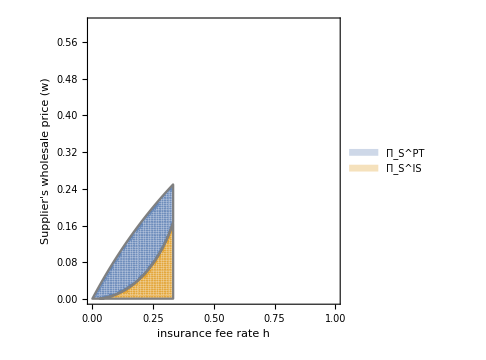

```mathematica
RegionPlot[{((πspt11>πsis1&&reg1a))&&w>c&&yi≥0,((πspt11≤πsis1&&reg1a))&&w>c&&yi≥0},{w,0.001,1},{h,0.001,0.6},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]
```

#### in the region that τpt^*=1-p/w √((3w-p-2c)/(-2c+p+w))

```mathematica
Clear[p,h,w,c]
```

```mathematica
aa2=πspt12-πsis1//FullSimplify
```

(-2 c+p+w)^2/(8 p)-(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))

(-2 c+p+w)^2/(8 p)-(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))>0,  (-2 c+p+w)^2/(8 p)>(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w)), ((-2 c+p+w)^2(p+w))/(4 p^2) >2(w-c)-2 w h+h^2 (p+w),  h>(w-c)/w+(h^2 (p+w))/(2w)-((p+w-2c)^2(p+w))/(8w p^2) =h_b(h,w,c)

c_1(w)≤c≤c_2(w)   h>h_b(h,w,c)

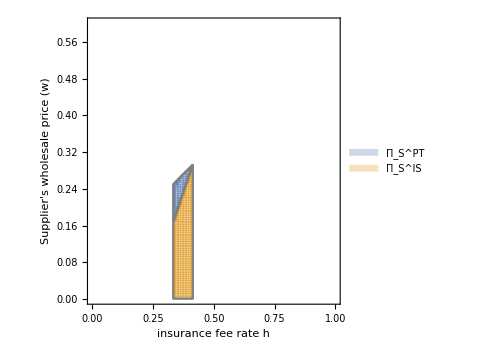

```mathematica
c=0;p=1;
RegionPlot[{((πspt12>πsis1&&reg2a))&&w>c&&yi≥0,((πspt12≤πsis1&&reg2a))&&w>c&&yi≥0},{w,0.001,1},{h,0.001,0.6},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]
```

#### both regions

```mathematica
Clear[h]
```

```mathematica
c=0;
```

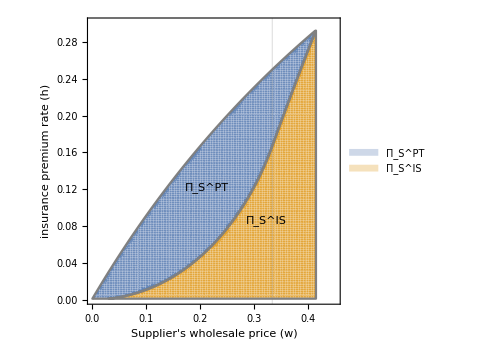
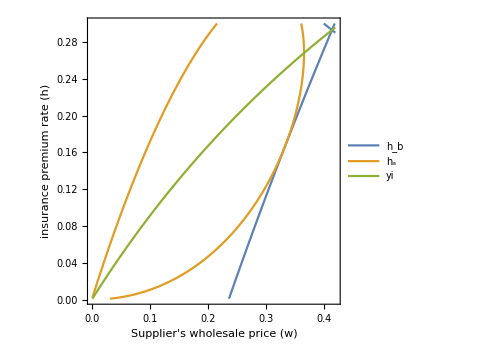

```mathematica
{RegionPlot[{Labeled[((πspt12>πsis1&&reg2a)||(πspt11>πsis1&&reg1a))&&w>c&&yi≥0,"Π_S^PT",Center,LabelStyle->Directive[15,Gray,Bold]],Labeled[((πspt12≤πsis1&&reg2a)||(πspt11≤πsis1&&reg1a))&&w>c&&yi≥0,"Π_S^IS",Center,LabelStyle->Directive[15,Gray,Bold]]},{w,0.001,0.45},{h,0.001,0.3},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's wholesale price (w)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium,GridLines->{{{0.3333,{Dashed,Gray,Thick}}},{}}],ContourPlot[{πspt12==πsis1,πspt11==πsis1,yi==0},{w,0.001,0.42},{h,0.001,0.3},PlotPoints->150,PlotLegends->{"h_b","h_a","yi"},FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's wholesale price (w)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]}
```

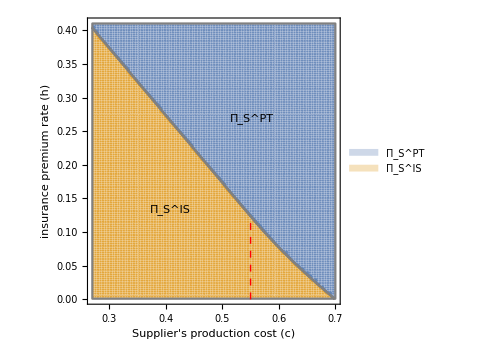
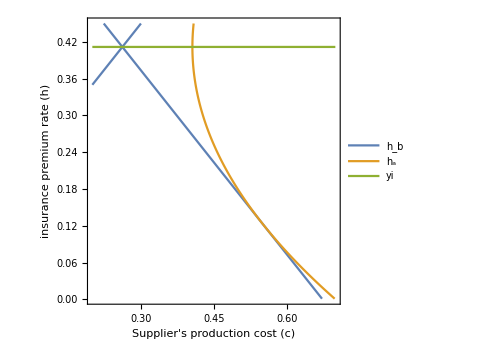

-Graphics-

```mathematica
Clear[c]
w=0.7;
{RegionPlot[{Labeled[((πspt12>πsis1&&reg2a)||(πspt11>πsis1&&reg1a))&&w>c&&yi≥0,"Π_S^PT",Center,LabelStyle->Directive[15,Gray,Bold]],Labeled[((πspt12≤πsis1&&reg2a)||(πspt11≤πsis1&&reg1a))&&w>c&&yi≥0,"Π_S^IS",Center,LabelStyle->Directive[15,Gray,Bold]]},{c,0.27,w},{h,0.001,0.41},PlotPoints->150,Epilog->{Red,Thick,Dashed,Line[{{c2,0},{c2,0.123529}}]},PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's production cost (c)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium],(*GridLines->{{{c2,{Dashed,Red,Thick}}},{}}],*)ContourPlot[{πspt12==πsis1,πspt11==πsis1,yi==0},{c,0.2,w},{h,0.001,0.45},PlotPoints->150,PlotLegends->{"h_b","h_a","yi"},FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's production cost (c)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]}
```

```mathematica
-Graphics-;
```

```mathematica
c1//N
c2//N
```

0.261765

0.55

```mathematica
(*Solve[{πspt12-πsis1==0,yi==0},{h,w}]//N*)
```

```mathematica
Solve[{πspt12-πsis1==0,πspt11-πsis1==0},{h,c}]//N
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{h→0.123529,c→0.55},{h→0.7,c→0.55}}

```mathematica
(*Solve[c1==0,w]//FullSimplify*)
```

```mathematica
(*Solve[c2==0,w]//FullSimplify*)
```

下面是想把边界用特殊格式表示，没成功

```mathematica
(*{RegionPlot[{((πspt12>πsis1&&reg2a)||(πspt11>πsis1&&reg1a))&&w>c&&yi≥0,((πspt12≤πsis1&&reg2a)||(πspt11≤πsis1&&reg1a))&&w>c&&yi≥0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,ImageSize->Medium,BoundaryStyle->None],ContourPlot[{πspt12==πsis1&&h≤0.292893,πspt11==πsis1,yi==0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,ImageSize->Medium,ContourStyle->{Directive[Lighter[Orange,0.4],Thick,Dashing[{0.03,0.01}]],Directive[Thick,Lighter[Red,0.4],Dashing[{0.03,0.01}]],Directive[Thick,GrayLevel[.7]],Directive[Thick,GrayLevel[.7],DotDashed]}]}*)
```

## 2

#### base

```mathematica
ClearAll["`*"]
```

```mathematica
πsft=p∫_0^((w qft)/p) (1-F[D])ⅆD-c qft;
πsis=p∫_0^((w qi-yi)/p) (1-F[D])ⅆD-c qi+(1-h)yi;
F[x_]:=x
Fm1[x_]:=x
```

```mathematica
πsft1=πsft/.qft->(p (p-w))/(p^2-w^2)//FullSimplify
```

(p (-2 c (p+w)+w (2 p+w)))/(2 (p+w)^2)

Under IS strategy , the supplier’s profit function

```mathematica
πsis1=πsis/.{qi->(p (p-w))/(p^2-w^2),yi->w (p (p-w))/(p^2-w^2)-p Fm1[h]}//FullSimplify
```

(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))

```mathematica
yi=w (p (p-w))/(p^2-w^2)-p Fm1[h]//FullSimplify
```

-h p+(p w)/(p+w)

#### Coparison

if IS strategy better than FT strategy, then yi>0,   -h p+(p w)/(p+w)>0, hp<(p w)/(p+w),  h< w/(p+w)   
h<w/(p+w)

```mathematica
c=0;p=1;
```

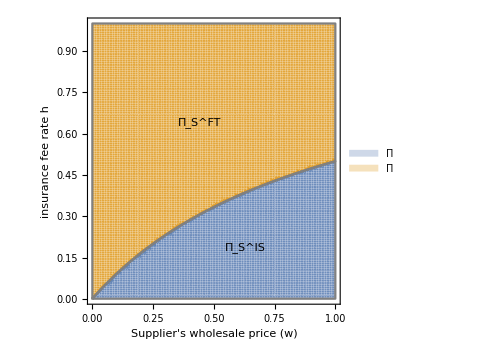

-Graphics-

```mathematica
RegionPlot[{Labeled[yi≥0&&w>c,"Π_S^IS",Center,LabelStyle->Directive[15,Gray,Bold]],Labeled[yi≤0&&w>c,"Π_S^FT",Center,LabelStyle->Directive[15,Gray,Bold]]},{w,0.001,1},{h,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["Π",FontFamily->"Times"],Style["Π",FontFamily->"Times"]},Above],FrameLabel->{{"insurance fee rate h",None},{"Supplier's wholesale price (w)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]
```

```mathematica
(*RegionPlot[{(πspt11>πsis1&&reg1a)&&w>c&&yi≥0,(πspt11≤πsis1&&reg1a)&&w>c&&yi≥0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]*)
```

## 3

#### base

```mathematica
ClearAll["`*"]
```

```mathematica
πsmts=p∫_0^(((1-τm)w qm-ym)/p) (1-F[D])ⅆD+τm w qm-c qm+(1-h)ym;
πspt=p∫_0^(((1-τpt)w qpt)/p) (1-F[D])ⅆD+τpt w qpt-c qpt;
F[x_]:=x
Fm1[x_]:=x
```

```mathematica
πspt1=πspt/.qpt->(p (p-w))/(p^2-w^2 (-1+τpt)^2)//FullSimplify;
```

for region c>c_2=1/2(3w-1) , the supplier’s profit function is

```mathematica
πspt11=πspt1/.τpt->1//FullSimplify
```

((p-w) (-c+w))/p

for region c_1≤c≤c_2 , c_1=1/2(1+w-2/(1+w))  the supplier’s profit function is

```mathematica
πspt12=πspt1/.τpt->1-p/w √((3w-p-2c)/(-2c+p+w))//FullSimplify
```

(-2 c+p+w)^2/(8 p)

Under IS strategy , the supplier’s profit function

```mathematica
πsmts1=(πsmts/.qm->(p (p-w))/(p^2-w^2 (-1+τm)^2))/.{τm->(√((c-h p-w) (c+h p-w) w^2)+w (c+(-1+h) w))/(h w^2),ym->(h p (2 c^2 w-2 h^2 p^2 w-4 c w^2+2 w^3-p √((c-h p-w) (c+h p-w) w^2)+w √((c-h p-w) (c+h p-w) w^2)))/(2 (c+h p-w) w (-c+h p+w))}//FullSimplify
```

(h^2 p^2 w+c w (-p+w)+(p-w) (w^2+√((c-h p-w) (c+h p-w) w^2)))/(2 p w)

#### in the region that τpt^*=1

if MTS strategy better than PT strategy, then

```mathematica
aa1=πsmts1-πspt11//FullSimplify
```

(h^2 p^2 w+c (p-w) w-(p-w) (w^2-√((c-h p-w) (c+h p-w) w^2)))/(2 p w)

if MTS>PT,  (h^2 p^2 w+c (p-w) w-(p-w) (w^2-√((c-h p-w) (c+h p-w) w^2)))/(2 p w)

```mathematica
c1=1/2(1+w-2(1+w));c2=1/2(3w-1);
reg1a=c>c2;reg2a=c≥c1&&c≤c2;
c=0.2;p=1;
ym[w_]:=(h p (2 c^2 w-2 h^2 p^2 w-4 c w^2+2 w^3-p √((c-h p-w) (c+h p-w) w^2)+w √((c-h p-w) (c+h p-w) w^2)))/(2 (c+h p-w) w (-c+h p+w));
τm[w_]:=(√((c-h p-w) (c+h p-w) w^2)+w (c+(-1+h) w))/(h w^2);
```

```mathematica
ff[a_]:=(w=a;Plot[{πsmts1,πspt11,πspt12},{h,0.001,1},PlotStyle->{Dashed,Red,Black},PlotLegends->"Expressions",ImageSize->Medium])
ffa[a_]:=(w=a;Plot[{ym[w],τm[w]},{h,0.001,1},PlotLegends->"Expressions",ImageSize->Medium])
Manipulate[{ff[w],ffa[w],c-1/2(3w-1)//N,c-1/2(1+w-2(1+w))},{w,c,1}]
Clear[w]
```

由图可以判断，用那个联立求解得出来的解的MTS策略也是始终小于PT策略的，所以MTS策略其实不存在，就写不存在吧

```mathematica
(*RegionPlot[{((πsmts1>πspt11&&reg1a))&&w>c,((πsmts1≤πspt12&&reg1a))&&w>c},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["Π_S^MTS",FontFamily->"Times"],Style["Π_S^PT",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance premium rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]*)
```

## 4

```mathematica
ClearAll["`*"]
```

```mathematica
πspt=p∫_0^(((1-τpt)w qpt)/p) (1-F[D])ⅆD+τpt w qpt-c qpt;
πsis=p∫_0^((w qi-yi)/p) (1-F[D])ⅆD-c qi+(1-h)yi;
F[x_]:=x
Fm1[x_]:=x
```

```mathematica
πspt1=πspt/.qpt->(p (p-w))/(p^2-w^2 (-1+τpt)^2)//FullSimplify;
```

for region c>c_2=1/2(3w-1) , the supplier’s profit function is

```mathematica
πspt11=πspt1/.τpt->1//FullSimplify
```

((p-w) (-c+w))/p

for region c_1≤c≤c_2 , c_1=1/2(1+w-2/(1+w))  the supplier’s profit function is

```mathematica
πspt12=πspt1/.τpt->1-p/w √((3w-p-2c)/(-2c+p+w))//FullSimplify
```

(-2 c+p+w)^2/(8 p)

Under IS strategy , the supplier’s profit function

```mathematica
πsis1=πsis/.{qi->(p (p-w))/(p^2-w^2),yi->w (p (p-w))/(p^2-w^2)-p Fm1[h]}//FullSimplify
```

(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))

#### in the region that τpt^*=1

if PT strategy better than IS strategy, then

```mathematica
aa1=πspt11-πsis1//FullSimplify
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))

```mathematica
-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))

```mathematica
Solve[aa1==0,c]//FullSimplify
```

{{c→-(h p^2)/w+w+(h^2 p^2 (p+w))/(2 w^2)}}

if PT>IS,  c> c_a(h,p,w)=-(h p^2)/w+w+(h^2 p^2 (p+w))/(2 w^2)

```mathematica
Solve[aa1==0,h]//FullSimplify
```

{{h→(w (p-√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))},{h→(w (p+√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))}}

```mathematica
Manipulate[{(w (p-√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w)),(w (p+√(p^2-2 p w-2 w^2+2 c (p+w))))/(p (p+w))},{p,1,1},{c,0,1},{w,0,1}];
```

-(h^2 p)/2+(h p w)/(p+w)+((c-w) w^2)/(p (p+w))>0,   (h p w)/(p+w)>(h^2 p)/2+((w-c) w^2)/(p (p+w)),  h> (h^2 p)/2*(p+w)/(p w)+((w-c) w^2)/(p (p+w))(p+w)/(p w)=h^2/2*(p+w)/w+((w-c) w)/p^2=h_a(h,w,c)

c>c_2(w)   h>h_a(h,w,c)

```mathematica
c1=1/2(1+w-2/(1+w));c2=1/2(3w-1);
reg1a=c>c2;reg2a=c≥c1&&c≤c2;
yi=w (p (p-w))/(p^2-w^2)-p Fm1[h];
c=0;p=1;
```

```mathematica
RegionPlot[{((πspt11>πsis1&&reg1a))&&w>c&&yi≥0,((πspt11≤πsis1&&reg1a))&&w>c&&yi≥0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]
```

-Graphics-

#### in the region that τpt^*=1-p/w √((3w-p-2c)/(-2c+p+w))

```mathematica
Clear[p,h,w,c]
```

```mathematica
aa2=πspt12-πsis1//FullSimplify
```

(-2 c+p+w)^2/(8 p)-(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))

(-2 c+p+w)^2/(8 p)-(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w))>0,  (-2 c+p+w)^2/(8 p)>(p (-2 c+2 w-2 h w+h^2 (p+w)))/(2 (p+w)), ((-2 c+p+w)^2(p+w))/(4 p^2) >2(w-c)-2 w h+h^2 (p+w),  h>(w-c)/w+(h^2 (p+w))/(2w)-((p+w-2c)^2(p+w))/(8w p^2) =h_b(h,w,c)

c_1(w)≤c≤c_2(w)   h>h_b(h,w,c)

```mathematica
c=0;p=1;
RegionPlot[{((πspt12>πsis1&&reg2a))&&w>c&&yi≥0,((πspt12≤πsis1&&reg2a))&&w>c&&yi≥0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]
```

-Graphics-

#### both regions

```mathematica
Clear[h]
```

```mathematica
Plot[c1,{w,0,1}]
```

-Graphics-

```mathematica
w=0.7;
```

```mathematica
{RegionPlot[{Labeled[(((πspt12>πsis1&&reg2a)||(πspt11>πsis1&&reg1a))&&w>c&&yi≥0)||(c≥c1&&yi<0),"Π_S^PT",Center,LabelStyle->Directive[15,Gray,Bold]],Labeled[(((πspt12≤πsis1&&reg2a)||(πspt11≤πsis1&&reg1a))&&w>c&&yi≥0)||(yi≥0&&c≤c1),"Π_S^IS",Center,LabelStyle->Directive[15,Gray,Bold]],Labeled[yi<0&&c<c1,"Π_S^FT",Center,LabelStyle->Directive[15,Gray,Bold]]},{c,0.001,w},{h,0.001,0.6},PlotPoints->150,Epilog->{{Red,Thick,Dashed,Line[{{c2,0},{c2,0.123529}}]},{Orange,Thick,Dashed,Line[{{c1,0},{c1,0.4102}}]}},PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's production cost (c)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium(*,GridLines->{{{c1,{Dashed,Gray,Thick}}},{}}*)],ContourPlot[{πspt12==πsis1,πspt11==πsis1,yi==0},{c,0.001,w},{h,0.001,0.6},PlotPoints->150,PlotLegends->{"h_b","h_a","yi"},FrameLabel->{{"insurance premium rate (h)",None},{"Supplier's wholesale price (w)",None}},PlotRangePadding->0,BoundaryStyle->Directive[Gray,Thin],ImageSize->Medium]}
```

{-Graphics-,-Graphics-}

-Graphics-

理论分析：
FT best:  when  c<c_1(w) and h≥w/(p+w)
PT best: when (1) c>c_2(w)  and h>h_a(h,w,c)    (2) c_1(w)≤c≤c_2(w) and h>h_b(h,w,c)
IS best: when (1)c<c_1(w) and h<w/(p+w)  (2) c>c_2(w)  and h≤h_a(h,w,c)    (3) c_1(w)≤c≤c_2(w) and h≤h_b(h,w,c)

```mathematica
Solve[{πspt12-πsis1==0,yi==0},{h,w}]//N
```

Solve::ivar: 0.7 is not a valid variable.

Solve[{0.36125-0.294118 (1.4-1.4 h+1.7 h^2)==0.,0.411765-1. h==0.},{h,0.7}]

```mathematica
Solve[{πspt12-πsis1==0,πspt11-πsis1==0},{h,w}]//N
```

Solve::ivar: 0.7 is not a valid variable.

Solve[{0.36125-0.294118 (1.4-1.4 h+1.7 h^2)==0.,0.21-0.294118 (1.4-1.4 h+1.7 h^2)==0.},{h,0.7}]

```mathematica
c1//FullSimplify
```

0.261765

```mathematica
c2//FullSimplify
```

0.55

下面是想把边界用特殊格式表示，没成功

```mathematica
(*{RegionPlot[{((πspt12>πsis1&&reg2a)||(πspt11>πsis1&&reg1a))&&w>c&&yi≥0,((πspt12≤πsis1&&reg2a)||(πspt11≤πsis1&&reg1a))&&w>c&&yi≥0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,PlotLegends->Placed[{Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(PT\)]\)",FontFamily->"Times"],Style["\!\(\*SubsuperscriptBox[\(Π\), \(S\), \(IS\)]\)",FontFamily->"Times"]},Above],FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,ImageSize->Medium,BoundaryStyle->None],ContourPlot[{πspt12==πsis1&&h≤0.292893,πspt11==πsis1,yi==0},{h,0.001,0.6},{w,0.001,1},PlotPoints->150,FrameLabel->{{"Supplier's wholesale price (w)",None},{"insurance fee rate h",None}},PlotRangePadding->0,ImageSize->Medium,ContourStyle->{Directive[Lighter[Orange,0.4],Thick,Dashing[{0.03,0.01}]],Directive[Thick,Lighter[Red,0.4],Dashing[{0.03,0.01}]],Directive[Thick,GrayLevel[.7]],Directive[Thick,GrayLevel[.7],DotDashed]}]}*)
```